```mathematica
SetDirectory[NotebookDirectory[]];

fun3[x_]=Piecewise[{{2x+5,0<= x<1/Pi},{((-5 Pi^2(x^2-2x-5))+10 Pi x+2x )/(1+5 Pi^2),1/Pi<=x<2/Pi},{(2 Sin[2 x]+((4+20 Pi^2+25 Pi^3)/(Pi+5 Pi^3)))-2 Sin[4/Pi],2/Pi<=x<=8/Pi}
}];
val = Integrate[fun3[x],{x,0.0,8/Pi}];

data1 = Import["f3Table1_FUNC1_TRAPE.txt","TABLE"];
data2 = Import["f3Table1_FUNC1_S_1_3.txt","TABLE"];
data3 = Import["f3Table1_FUNC1_S_8_3.txt","TABLE"];
data4 = Import["f3Table1_FUNC1_GAUSS.txt","TABLE"];

xcord=1;
ycord=3;
cerror=3;
ctasas=4;

data11=Table[{data1[[i,cerror]],data1[[i,ctasas]]},{i,1,Length[data1],1}];
data12=Table[{data2[[i,cerror]],data2[[i,ctasas]]},{i,1,Length[data2],1}];
data13=Table[{data3[[i,cerror]],data3[[i,ctasas]]},{i,1,Length[data3],1}];
data14=Table[{data4[[i,cerror]],data4[[i,ctasas]]},{i,1,Length[data4],1}];

data1ToPlot = Table[{data1[[i,xcord]],data1[[i,ycord]]},{i,1,Length[data1],1}];
data2ToPlot = Table[{data2[[i,xcord]],data2[[i,ycord]]},{i,1,Length[data2],1}];
data3ToPlot = Table[{data3[[i,xcord]],data3[[i,ycord]]},{i,1,Length[data3],1}];
data4ToPlot = Table[{data4[[i,xcord]],data4[[i,ycord]]},{i,1,Length[data4],1}];
colors = {{Red},{Blue}, {Green}, {Black}};
colors1 = {{Red,Dashed},{Blue,Dashed}, {Green,Dashed}, {Brown,Dashed}};
namestoplot={Style["M. Gauss-Legendre",12],Style["M. Simpson 1/3",12],Style["M. Simpson 3/8",12],Style["M. Gauss Legendre",12]};
format = {PlotStyle->colors,PlotLegends->namestoplot,Frame->True,FrameLabel->{"Log h","Log erro"} ,FrameStyle->Directive[Black, Thickness[0.005],Bold,FontSize->16],FrameTicksStyle->{{FontSize->15,Black},{FontSize->15,Black},{FontSize->15,Black},{FontSize->15,Black}},GridLines->Automatic};
```

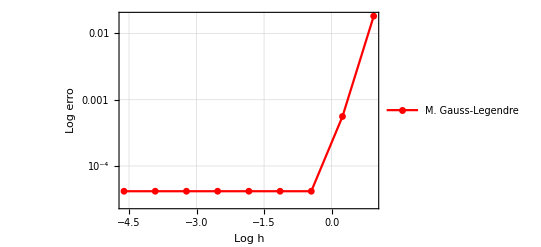

P4_Funcion3.pdf

F3_TRAPECIOS.xlsx

F3_SIMP_1_3.xlsx

F3_SIMP_3_8.xlsx

F3_GAUSS.xlsx

```mathematica
plot1 = ListLogPlot[data4ToPlot,Joined->True, PlotRange->All,format, PlotMarkers->{Automatic, Small}]

(*plot1 = ListLogPlot[{ data1ToPlot,data2ToPlot,data3ToPlot,data4ToPlot},Joined->True, PlotRange->All,format, PlotMarkers->{Automatic, Small}]*)
Export["P4_Funcion3.pdf",plot1]
Export["F3_TRAPECIOS.xlsx",data11]
Export["F3_SIMP_1_3.xlsx",data12]
Export["F3_SIMP_3_8.xlsx",data13]
Export["F3_GAUSS.xlsx",data14]
```

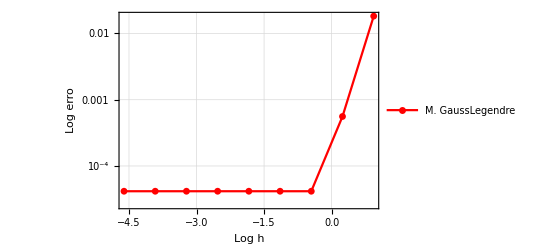

P4_Funcion3.pdf

F3_TRAPECIOS.xlsx

F3_SIMP_1_3.xlsx

F3_SIMP_3_8.xlsx

F3_GAUSS.xlsx